```mathematica
FSize1=30;
FSize2=24;
FontUse="Times";
```

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\"<>"output"];
rvout = Import["rvoutcreep.dat","Table"];
eout=Import["einpoly.dat","Table"];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\"<>"input\\experiment"];
exp1 = Import["exo800.txt","Table"];
exp2 = Import["exo850.txt","Table"];
fem=Import["FEM.txt","Table"];
```

```mathematica
rvtestcrush10= Table[{rvout[[i,6]]/7200,rvout[[i,1]]*100},{i,1,Length[rvout]}];
```

```mathematica
rvtestsl= Table[{rvout[[i,6]]/3600,rvout[[i,2]]*100*10^3},{i,1,Length[rvout]}];
rvtestcl= Table[{rvout[[i,6]]/3600,rvout[[i,3]]*100*10^3},{i,1,Length[rvout]}];
rvtestdiff= Table[{rvout[[i,6]]/3600,rvout[[i,4]]*100*10^3},{i,1,Length[rvout]}];
```

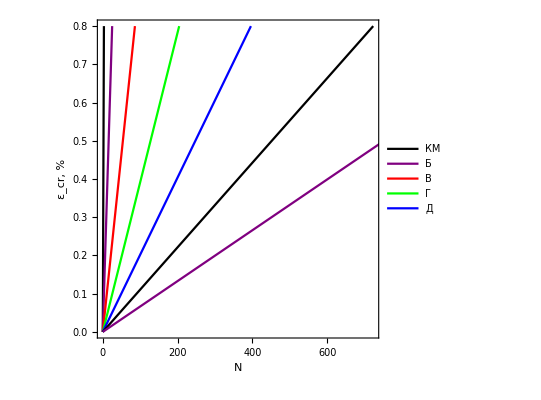

```mathematica
Img=ListLinePlot[{rvtestcrush10,rvtestcrush20,rvtestcrush30,rvtestcrush40,rvtestcrush50,rvtestcrush60,rvtestcrush70} ,PlotRange-> {{0,723},{0,0.8}},Axes->True,PlotLegends->Placed[{"КМ","Б","В","Г","Д"},Above],Frame->True,FrameLabel->{Style["N",FSize1, FontFamily->"Times"],Style["ε_cr, %",FSize1, FontFamily->"Times"]}, PlotStyle->{{Black,Thick},{Purple,Thick},{Red,Thick},{Green,Thick},{Blue,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.5],AspectRatio->1];
Img0=ListPlot[{exp2} ,PlotRange-> {{0,20},{0,3}},Axes->True,PlotLegends->Placed[{"Эксперимент","Б","В","Г","Д"},Above],Frame->True,FrameLabel->{Style["t, ч",FSize1, FontFamily->"Times"],Style["ε_cr, %",FSize1, FontFamily->"Times"]}, PlotStyle->{{Black,Thick},{Purple,Thick},{Red,Thick},{Green,Thick},{Blue,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.5],AspectRatio->1];
ForExp=Show[Img]
```

```mathematica
(*Export["G:\\Мой диск\\Научка\\ПИШ\\Ползучесть\\Для отчета\\Рисунок 3.3 Б.txt",rvtestIni]*)
```

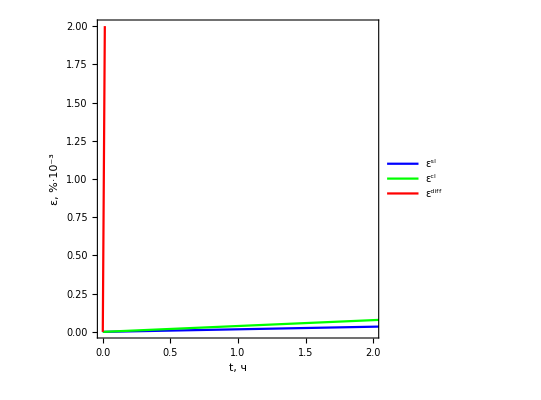

```mathematica
Img=ListLinePlot[{rvtestsl,rvtestcl,rvtestdiff} ,PlotRange-> {{0,2},{0,2}},Axes->True,PlotLegends->Placed[{"ε^sl","ε^cl","ε^diff"},Above],Frame->True,FrameLabel->{Style["t, ч",FSize1, FontFamily->"Times"],Style["ε, %·10^-3",FSize1, FontFamily->"Times"]}, PlotStyle->{{Blue,Thick},{Green,Thick},{Red,Thick},{Purple,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.5],AspectRatio->1];
ForExp=Show[Img]
```

```mathematica
(*Export["G:\\Мой диск\\Научка\\ПИШ\\Ползучесть\\Для отчета\\Рисунок 3.7 Cdiff.txt",rvtestdiff]*)
```

```mathematica
Last[TakeWhile[rvtestcrush70,#[[2]]<=0.8&]]
```

{1203,0.79999}

```mathematica
KK={{10,3},{20,25},{30,86},{40,204},{50,400},{60,723},{70,1203}};
```

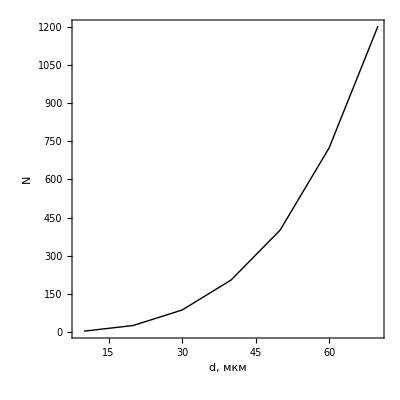

```mathematica
Img=ListLinePlot[{KK} ,PlotRange-> {All,All},Axes->True,Frame->True,FrameLabel->{Style["d, мкм",FSize1, FontFamily->"Times"],Style["N",FSize1, FontFamily->"Times"]}, PlotStyle->{{Black,Thick},{Green,Thick},{Red,Thick},{Purple,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.5],AspectRatio->1]
```

```mathematica
(*Export["G:\\Мой диск\\Научка\\ПИШ\\Ползучесть\\Для отчета\\Рисунок 3.8.txt",KK]*)
```

G:\Мой диск\Научка\ПИШ\Ползучесть\Для отчета\Рисунок 3.8.txt

```mathematica
rvtestcl={ {0,0.},
{1,0.19841999999999999},
{2,0.39682999999999996},
{3,0.59525},
{4,0.7936599999999999},
{5,0.9920800000000001}};
rvtestsl= {{0,0.},
{1,2.5452},
{2,5.0904},
{3,7.635700000000001},
{4,10.181},
{5,12.725999999999999}};
rvtestdiff={ {0,0.},
{1,2.1755999999999998},
{2,4.3511999999999995},
{3,6.5269},
{4,8.7025},
{5,10.878}};
```

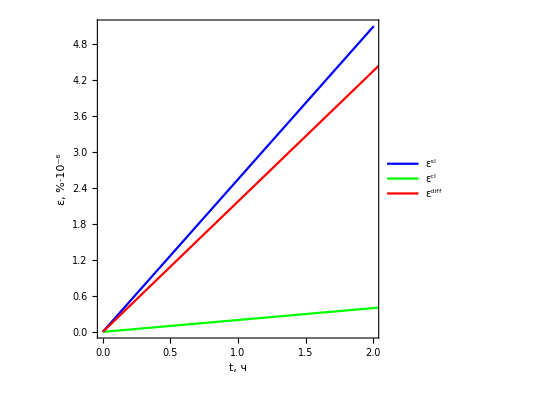

```mathematica
Img=ListLinePlot[{rvtestsl,rvtestcl,rvtestdiff} ,PlotRange-> {{0,2},{0,5.1}},Axes->True,PlotLegends->Placed[{"ε^sl","ε^cl","ε^diff"},Above],Frame->True,FrameLabel->{Style["t, ч",FSize1, FontFamily->"Times"],Style["ε, %·10^-6",FSize1, FontFamily->"Times"]}, PlotStyle->{{Blue,Thick},{Green,Thick},{Red,Thick},{Purple,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.5],AspectRatio->1];
ForExp=Show[Img]
```

```mathematica
(*Export["G:\\Мой диск\\Научка\\ПИШ\\Ползучесть\\Для отчета\\Рисунок 3.7 B.jpg",ForExp]*)
```

G:\Мой диск\Научка\ПИШ\Ползучесть\Для отчета\Рисунок 3.7 B.jpg

```mathematica
rvtest11= Table[{rvout[[i,6]]/3600,eout[[i,1]]*100},{i,1,Length[rvout]}];
rvtest22= Table[{rvout[[i,6]]/3600,eout[[i,5]]*100},{i,1,Length[rvout]}];
rvtest33= Table[{rvout[[i,6]]/3600,eout[[i,9]]*100},{i,1,Length[rvout]}];
rvtest12= Table[{rvout[[i,6]]/3600,(eout[[i,2]]+eout[[i,4]])/2*100},{i,1,Length[rvout]}];
rvtest13= Table[{rvout[[i,6]]/3600,(eout[[i,3]]+eout[[i,7]])/2*100},{i,1,Length[rvout]}];
rvtest23= Table[{rvout[[i,6]]/3600,(eout[[i,6]]+eout[[i,8]])/2*100},{i,1,Length[rvout]}];
```

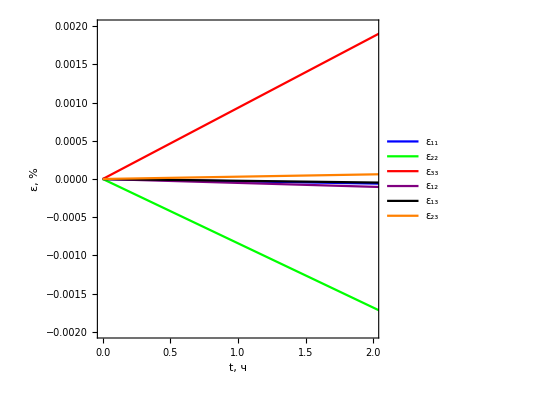

```mathematica
Img=ListLinePlot[{rvtest11,rvtest22,rvtest33,rvtest12,rvtest13,rvtest23} ,PlotRange-> {{0,2},{-2 10^-3,2 10^-3}},Axes->True,PlotLegends->Placed[{"ε_11","ε_22","ε_33","ε_12","ε_13","ε_23"},Above],Frame->True,FrameLabel->{Style["t, ч",FSize1, FontFamily->"Times"],Style["ε, %",FSize1, FontFamily->"Times"]}, PlotStyle->{{Blue,Thick},{Green,Thick},{Red,Thick},{Purple,Thick},{Black,Thick},{Orange,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.5],AspectRatio->1]
```

```mathematica
fem11= Table[{fem[[i,1]]/3600,-fem[[i,2]]*100*10^3},{i,1,Length[fem]}];
fem22= Table[{fem[[i,1]]/3600,-fem[[i,3]]*100*10^3},{i,1,Length[fem]}];
fem33= Table[{fem[[i,1]]/3600,-fem[[i,4]]*100*10^3},{i,1,Length[fem]}];
fem12= Table[{fem[[i,1]]/3600,-fem[[i,5]]*100*10^3},{i,1,Length[fem]}];
fem13= Table[{fem[[i,1]]/3600,-fem[[i,6]]*100*10^3},{i,1,Length[fem]}];
fem23= Table[{fem[[i,1]]/3600,-fem[[i,7]]*100*10^3},{i,1,Length[fem]}];
```

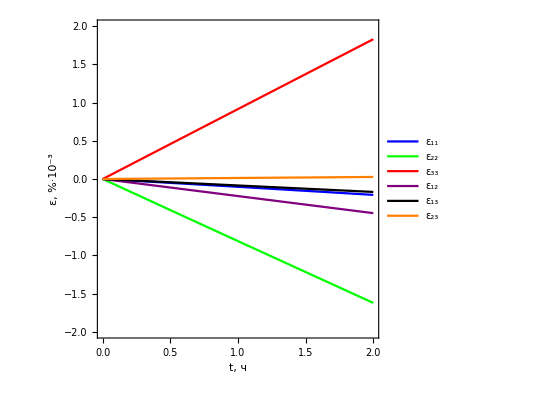

```mathematica
Img=ListLinePlot[{fem11,fem22,fem33,fem12,fem13,fem23} ,PlotRange-> {{0,2},{-2,2 }},Axes->True,PlotLegends->Placed[{"ε_11","ε_22","ε_33","ε_12","ε_13","ε_23"},Above],Frame->True,FrameLabel->{Style["t, ч",FSize1, FontFamily->"Times"],Style["ε, %·10^-3",FSize1, FontFamily->"Times"]}, PlotStyle->{{Blue,Thick},{Green,Thick},{Red,Thick},{Purple,Thick},{Black,Thick},{Orange,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.5],AspectRatio->1]
```

```mathematica
Export["G:\\Мой диск\\Научка\\ПИШ\\Ползучесть\\Для отчета\\Рисунок 3.9 B.jpg",Img]
```

G:\Мой диск\Научка\ПИШ\Ползучесть\Для отчета\Рисунок 3.9 B.jpg